```mathematica
Table[allGraphs[k,"graph"],{k,allGraphs[alfa1Key,"parents"]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allGraphs[alfaKey,"graph"]
```

-Graphics-

```mathematica
Table[allGraphs[k,"comp"]=Equal;allGraphs[k,"compwhy"]="assumption",{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{assumption,assumption,assumption,assumption,assumption}

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PushAllGraphs[]
```

0

```mathematica
PushAllGraphs2[keys_]:=Block[{leftKey,rightKey,left,right,current,children,changed=0},
Monitor[
Table[
current = allGraphs[k];
If[ToString[current["comp"]]=="Greater" ,
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs[leftKey];
right=allGraphs[rightKey];
If[ToString[left["comp"]]=="Equal"&&ToString[right["comp"]]=="GreaterEqual",
right["comp"]=Greater;
right["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (so this must be >0)";
Print[right["compwhy"]];
changed++;
allGraphs[rightKey]=right;
];
If[ToString[right["comp"]]=="Equal"&&ToString[left["comp"]]=="GreaterEqual",
left["comp"]=Greater;
left["compwhy"]="The relation holds x"<> ToString[k]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (so this must be >0)";
Print[left["compwhy"]];
changed++;
allGraphs[leftKey]=left;
],
{children,allGraphs[k,"children"]}]
]
,
{k,keys}],
k
];
changed
]
```

```mathematica
PushAllGraphs2[Keys[allGraphs]]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
Map[{VertexCount[allGraphs[#,"graph"]],allGraphs[#,"comp"]}&,Keys[allGraphs]]//Tally
```

{{{5,Greater},1013},{{5,GreaterEqual},10},{{5,Equal},1},{{4,GreaterEqual},5},{{4,Greater},635},{{3,Greater},170},{{3,GreaterEqual},25},{{3,Equal},5},{{2,Greater},25},{{2,GreaterEqual},5},{{1,Greater},1}}

```mathematica
weirdos=Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==5 && allGraphs[#,"comp"]==GreaterEqual]&]
```

{29523,29514,29515,29281,29272,28794,28795,9841,9598,9112}

```mathematica
treeForm5[lambdaKey,"colofour"]/.repcolofour5base
```

-Graphics-v13x24x5+-Graphics-v13x25x4+-Graphics-v1x24x35+-Graphics-v14x25x3+-Graphics-v14x2x35+-Graphics-v1x24x3x5+-Graphics-v1x25x3x4+-Graphics-v1x2x35x4+-Graphics-v13x2x4x5+-Graphics-v14x2x3x5+-Graphics-v1x2x3x4x5

```mathematica
Table[Framed[Labeled[allGraphs[k,"graph"],{allGraphs[k,"colofour"]/.repZero/.repcolofour5base,Style[k,ColourForKey[allGraphs,k]]},{Bottom,Top}]],{k,weirdos}]
```

{-Graphics--Graphics-v1x2x3x4529523,-Graphics--Graphics-v1x2x34x5+-Graphics-v1x2x3x4529514,-Graphics--Graphics-v1x2x34x529515,-Graphics--Graphics-v1x23x4x529281,-Graphics--Graphics-v1x23x4x5+-Graphics-v1x2x34x529272,-Graphics--Graphics-v1x2x3x45+-Graphics-v15x2x3x428794,-Graphics--Graphics-v15x2x3x428795,-Graphics--Graphics-v12x3x4x59841,-Graphics--Graphics-v1x23x4x5+-Graphics-v12x3x4x59598,-Graphics--Graphics-v12x3x4x5+-Graphics-v15x2x3x49112}

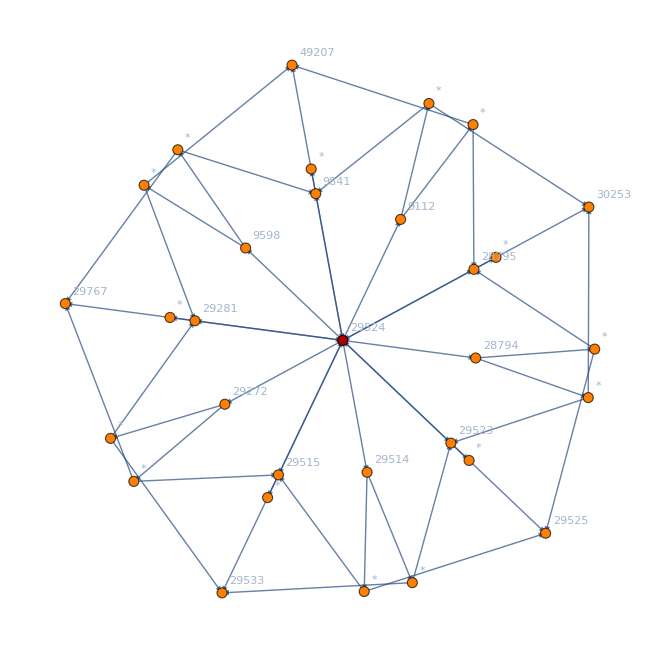

```mathematica
Graph[DependencyGraph[allGraphs,weirdos],GraphLayout->"HighDimensionalEmbedding"]
```

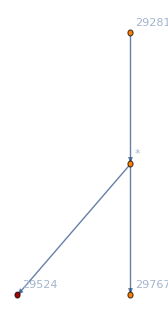

```mathematica
Graph[DependencyGraph[allGraphs,29281],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Table[allGraphs[k,"comp"],{k,Keys[allGraphs]}]//Tally
```

{{Greater,1844},{GreaterEqual,45},{Equal,6}}

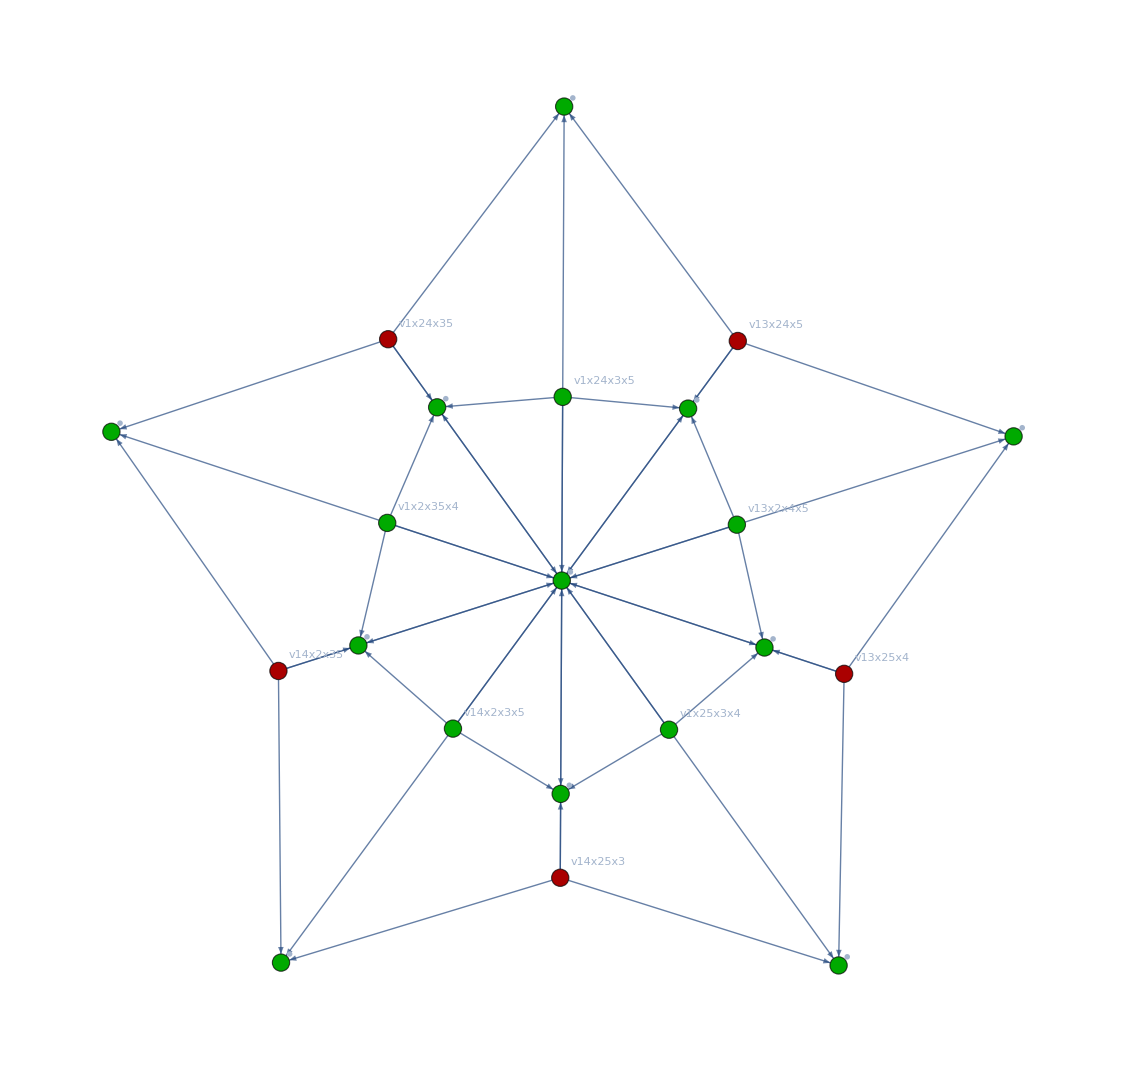

```mathematica
Graph[ExpressionsToGraph[Join[Select[PositiveExpressions,Length[#]>2&],{allGraphs[lambdaKey,"colofour"]}]],GraphLayout->"HighDimensionalEmbedding",ImageSize->600]
```

```mathematica
Graph[ExpressionsToGraph[Select[PositiveExpressions,Length[#]>2&]],GraphLayout->"HighDimensionalEmbedding",ImageSize->600]
```

```mathematica
TableForm[Table[{allGraphs[k,"graph"],Factor[{GraphAutomorphismGroup[allGraphs[k,"graph"]]//GroupOrder,ChromaticPolynomial[allGraphs[k,"graph"],4]/24}]},{k,{35977,36085}}],TableDepth->3]
```

-Graphics- | {2}
{3}
-Graphics- | {24}
{1}

```mathematica
FlowPolynomial[CompleteGraph[3],x]
```

-1+x

```mathematica
FindGraphIsomorphism
```

```mathematica
Graph[ExpressionsToGraph[Join[Select[PositiveExpressions,Length[#]==2&],{allGraphs[lambdaKey,"colofour"]}]],GraphLayout->"HighDimensionalEmbedding",ImageSize->600]
```

```mathematica
treeForm5["full","graph"]
```

-Graphics-

```mathematica
Graph[DualGraph[Faces[EmbedGraph5Bis[allGraphs,alfa1Key]]],GraphLayout->"PlanarEmbedding"]
```